```mathematica
ClearAll["Global`*"];

pts = {{0, 2}, {2, 4}, {3, 6}, {5,-2}}

method = "Natural"
(* method is either "Natural" or "Clamped"; *)

mLeft = 0;
mRight = 0;
```

{{0,2},{2,4},{3,6},{5,-2}}

Natural

```mathematica
x = pts[[All, 1]]
```

{0,2,3,5}

```mathematica
y = pts[[All, 2]]
```

{2,4,6,-2}

```mathematica
n = Length[pts] - 1
```

3

```mathematica
s = Table[
   a[i] + b[i] (t - x[[i]]) +
    c[i] (t - x[[i]])^2 +
    d[i] (t - x[[i]])^3,
   {i, n}
   ]
```

{a[1]+t b[1]+t^2 c[1]+t^3 d[1],a[2]+(-2+t) b[2]+(-2+t)^2 c[2]+(-2+t)^3 d[2],a[3]+(-3+t) b[3]+(-3+t)^2 c[3]+(-3+t)^3 d[3]}

```mathematica
eq1 = Flatten@Table[
    {
     (s[[i]] /. t -> x[[i]]) == y[[i]],
     (s[[i]] /. t -> x[[i + 1]]) == y[[i + 1]]
     },
    {i, n}
    ]
```

{a[1]==2,a[1]+2 b[1]+4 c[1]+8 d[1]==4,a[2]==4,a[2]+b[2]+c[2]+d[2]==6,a[3]==6,a[3]+2 b[3]+4 c[3]+8 d[3]==-2}

```mathematica
eq2 = Table[
   (D[s[[i]], t] /. t -> x[[i + 1]]) ==
    (D[s[[i + 1]], t] /. t -> x[[i + 1]]),
   {i, n - 1}
   ]
```

{b[1]+4 c[1]+12 d[1]==b[2],b[2]+2 c[2]+3 d[2]==b[3]}

```mathematica
eq3 = Table[
   (D[s[[i]], {t, 2}] /. t -> x[[i + 1]]) ==
    (D[s[[i + 1]], {t, 2}] /. t -> x[[i + 1]]),
   {i, n - 1}
   ]
```

{2 c[1]+12 d[1]==2 c[2],2 c[2]+6 d[2]==2 c[3]}

```mathematica
eq4 = Switch[
   method,

   "Natural",
   {
    (D[s[[1]], {t, 2}] /. t -> x[[1]]) == 0,
    (D[s[[-1]], {t, 2}] /. t -> x[[-1]]) == 0
    },

   "Clamped",
   {
    (D[s[[1]], t] /. t -> x[[1]]) == mLeft,
    (D[s[[-1]], t] /. t -> x[[-1]]) == mRight
    },

   _,
   Print["Error: method must be \"Natural\" or \"Clamped\"."]
   ]
```

{2 c[1]==0,2 c[3]+12 d[3]==0}

```mathematica
unknowns = Flatten@Table[
    {a[i], b[i], c[i], d[i]},
    {i, n}
    ]
```

{a[1],b[1],c[1],d[1],a[2],b[2],c[2],d[2],a[3],b[3],c[3],d[3]}

```mathematica
sol = Solve[
   Join[eq1, eq2, eq3, eq4],
   unknowns
   ]
```

{{a[1]→2,b[1]→11/35,c[1]→0,d[1]→6/35,a[2]→4,b[2]→83/35,c[2]→36/35,d[2]→-7/5,a[3]→6,b[3]→8/35,c[3]→-111/35,d[3]→37/70}}

```mathematica
spline = Simplify[s /. First[sol]]
```

{1/35 (70+11 t+6 t^3),1/35 (510-649 t+330 t^2-49 t^3),1/70 (-2625+2347 t-555 t^2+37 t^3)}

```mathematica
pw = Piecewise[
   Table[
    {
     spline[[i]],
     x[[i]] <= t <= x[[i + 1]]
     },
    {i, n}
    ]
   ]
```

Piecewise[{{1/35 (70+11 t+6 t^3), 0≤t≤2}, {1/35 (510-649 t+330 t^2-49 t^3), 2≤t≤3}, {1/70 (-2625+2347 t-555 t^2+37 t^3), 3≤t≤5}, {0, True}}]

```mathematica
nodeSym = Table[Subscript[t, i], {i, n + 1}];
sSym = Table[
   a[i] + b[i] (t - nodeSym[[i]]) + c[i] (t - nodeSym[[i]])^2 +
    d[i] (t - nodeSym[[i]])^3,
   {i, n}
   ];
pwSym = Piecewise[
   Table[
    {sSym[[i]] /. First[sol], x[[i]] <= t <= x[[i + 1]]},
    {i, n}
    ]
   ]
```

Piecewise[{{2+11/35 (t-t_1)+6/35 (t-t_1)^3, 0≤t≤2}, {4+83/35 (t-t_2)+36/35 (t-t_2)^2-7/5 (t-t_2)^3, 2≤t≤3}, {6+8/35 (t-t_3)-111/35 (t-t_3)^2+37/70 (t-t_3)^3, 3≤t≤5}, {0, True}}]

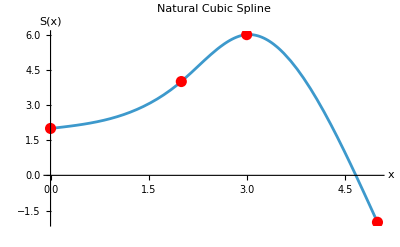

```mathematica
Plot[
 pw,
 {t, x[[1]], x[[-1]]},
 PlotRange -> All,
 Epilog -> {
   Red,
   PointSize[0.02],
   Point[pts]
   },
 AxesLabel -> {"x", "S(x)"},
 PlotLabel -> method <> " Cubic Spline"
]
```